```mathematica
(* Visualization of the posterior density with two stimuli {Subscript[x, 1],Subscript[x, 2]} and dichotomous outcome {s,f} *)
```

## Example with binomial data

```mathematica
(* Data *)
L=2;
successes={2,3};
failures = {5,3};
(* Parameters *)
σ=1; (* in the paper: α = (σ, γ) *)
γ=1;
```

## Full posterior density function

```mathematica
fd[bij_]:=Module[{i,j},
{i,j}=bij/.Subscript[b, i_,j_]->{i,j};
1/Beta[σ,γ] Subscript[p, i,j]^(ns[bij]+σ-1)(1-Subscript[p, i,j])^(nf[bij]+γ-1)]
```

```mathematica
f[p1_,p2_,"|B1,D"]:=If[p1==p2,(prombs[A[L],fd,P["B"],L]/prombs[A[L],fe,P["B"],L])[[1]]/.Subscript[p, 1,2]->p1,0]
f[p1_,p2_,"|B2,D"]:=(prombs[A[L],fd,P["B"],L]/prombs[A[L],fe,P["B"],L])[[2]]/.{Subscript[p, 1,1]->p1,Subscript[p, 2,2]->p2}
```

## Full posterior plots

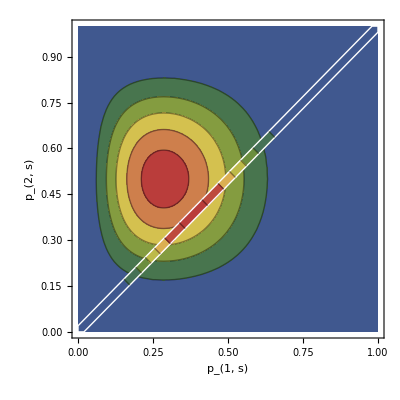

```mathematica
Show[
ContourPlot[f[x,y,"|B2,D"],{x,0,1},{y,0,1},ColorFunction->"DarkRainbow"],
ContourPlot[f[(x+y)/2,(x+y)/2,"|B1,D"],{x,0,1},{y,0,1},RegionFunction->Function[{x,y,z},Abs[x-y]≤0.02],BoundaryStyle->White,ColorFunction->"DarkRainbow"],FrameLabel->{"p_(1, s)","p_(2, s)"},RotateLabel->False]
```

```mathematica
PlotMixedDensity[y_, options_:{}]:=
Show[
Graphics[Arrow[{{y,0},{y,f[y,y,"|B1,D"]}}]],
Plot[f[x,y,"|B2,D"],{x,0,1}],Frame->True,AspectRatio->1/2 (√5-1),options]
```

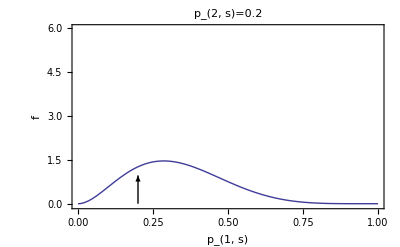

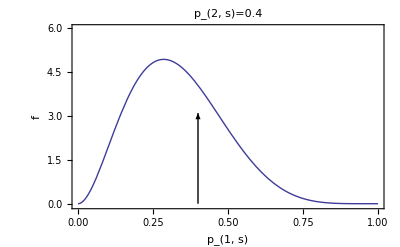

```mathematica
PlotMixedDensity[0.2,{PlotLabel-> "p_(2, s)=0.2",FrameLabel->{"p_(1, s)","f"},RotateLabel->False,PlotRange->{{0,1},{-0.05,6}}}]
PlotMixedDensity[0.4,{PlotLabel-> "p_(2, s)=0.4",FrameLabel->{"p_(1, s)","f"},RotateLabel->False,PlotRange->{{0,1},{-0.05,6}}}]
```

```mathematica
(*
1) The shape of the density (if normalized) for B1 is identical at each Subscript[p, 2,s] because it's a simple product density.
2) But there is a dependency on Subscript[p, 2] which expresses itself in the relative size of density and dirac peak for the second model B2 (of course also the position of the peak varies
*)
```

## Marginal posterior density function

```mathematica
(* marginal density for Subscript[x, 1] *)
fdp1[bij_]:=Module[{i,j},
{i,j}=bij/.Subscript[b, i_,j_]->{i,j};
If[i≤1≤j,fd[bij]/.Subscript[p, i,j]->p,fe[bij]]]
(* marginal density for Subscript[x, 2] *)
fdp2[bij_]:=Module[{i,j},
{i,j}=bij/.Subscript[b, i_,j_]->{i,j};
If[i≤2≤j,fd[bij]/.Subscript[p, i,j]->p,fe[bij]]]
```

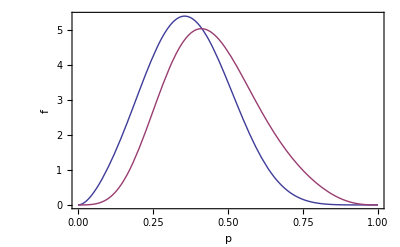

```mathematica
Plot[{Plus@@(prombs[A[L],fdp1,P["B"],L]/prombs[A[L],fe,P["B"],L]),Plus@@(prombs[A[L],fdp2,P["B"],L]/prombs[A[L],fe,P["B"],L])},{p,0,1},Frame->True,FrameLabel->{"p","f"},RotateLabel->False]
```